```mathematica
SetDirectory[NotebookDirectory[]];$PlotTheme="Scientific";texStyle={FontFamily->"Latin Modern Roman", FontSize->12};

Needs["MaTeX`"];

Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["NumericalCalculus`"];
(*$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`45."&);*)
CoolColors=(ColorData[97,"ColorList"]);
```

Background geometry - Slow-roll inflation and reheating (no Higgs backreaction)

### Units and parameters

```mathematica
(* Let us give some values *) (* From 2303.07359v2 *)

(*rMP=1;*)
(*rMP=2.435*10^18*) (* In GeV *)
rMP=2.435*10^18/(1.0*10^13) (* In 10^13 GeV *)(* In units of the inflaton mass for a quadratic potential *)
MP=rMP*Sqrt[8*Pi];
ne=55;

λS =2.5*10^-7/ne^2;
λT=6.2*10^-8/ne^2;
```

243500.

```mathematica
λS
```

8.26446×10^-11

```mathematica
rMP^4
```

3.51557×10^21

### Potential definition

```mathematica
(* Let us define first the inflationary potentials *)

VS[ϕ_]:=3/2*λS*rMP^4*(1-Exp[-Sqrt[2/3]*ϕ/rMP])^2
dVS[ϕ_]:=Sqrt[6]*λS*rMP^3(1-Exp[-Sqrt[2/3]*ϕ/rMP])*Exp[-Sqrt[2/3]*ϕ/rMP]
VT[ϕ_]:=λT*rMP^4*(Sqrt[6]*Tanh[ϕ/(Sqrt[6]*rMP)])^2
dVT[ϕ_]:=2*Sqrt[6]*λT*rMP^3*Sinh[ϕ/(Sqrt[6]*rMP)]/Cosh[ϕ/(Sqrt[6]*rMP)]^3
```

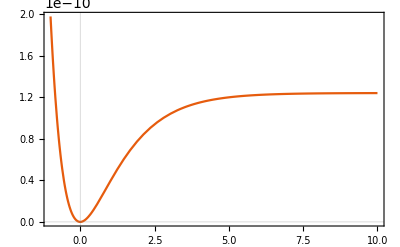

```mathematica
Plot[VS[x],{x,-1,10}]
```

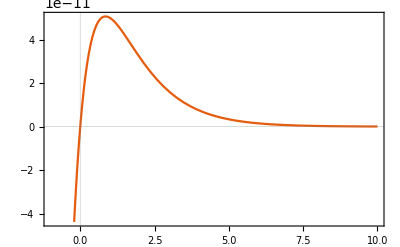

```mathematica
Plot[dVS[x],{x,-1,10}]
```

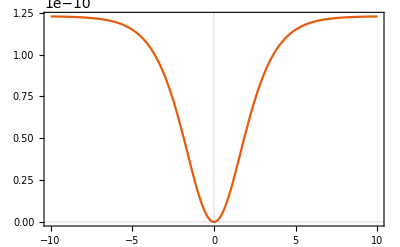

```mathematica
Plot[VT[x],{x,-10,10}]
```

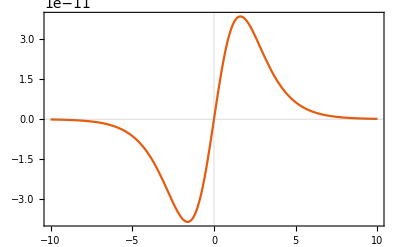

```mathematica
Plot[dVT[x],{x,-10,10}]
```

```mathematica
ϕi
```

5.45292

### Starobinsky

#### Solve for the inflaton field

```mathematica
(* Let us give the inflaton time evolution *)

(* First, the initial conditions *)

ti=-100*10^5/rMP;
tf=10^2*10^5/rMP;

ϕi=1.0877*MP;
dϕi=0;

(* Out of SR, we have to solve this numerically *)

HC[t_]=Sqrt[4*Pi/(3*MP^2)*(ϕn'[t]^2 + 2*VS[ϕ]/.ϕ->ϕn[t])];
EoM[t_]=ϕn''[t]+3*HC[t]*ϕn'[t] + dVS[ϕ]/.ϕ->ϕn[t];
ϕC[t_]=ϕn[t]/.NDSolve[{EoM[t]==0, ϕn[ti]==ϕi, ϕn'[ti]==dϕi}, {ϕn}, {t, ti, tf}][[1,1]];

(* We give the Ricci scalar for both regimes *)

RC[t_]=8*Pi/MP^2*(4*VS[ϕC[t]] - ϕC'[t]^2);
Ri=RC[ti];
```

```mathematica
NDSolve[{EoMS[t]==0, ϕn[ti]==ϕi, ϕn'[ti]==dϕi}, {ϕn}, {t, ti, tf}]
```

{{ϕn→Function[{t},1.32779×10^6]}}

```mathematica
(* The time-dependent hubble rate is given by the inflaton field *)

HC[t_]=Sqrt[4*Pi/(3*MP^2)*(ϕC'[t]^2 + 2*VS[ϕC[t]])];

Hi=HC[ti];
Hf = HC[0];
```

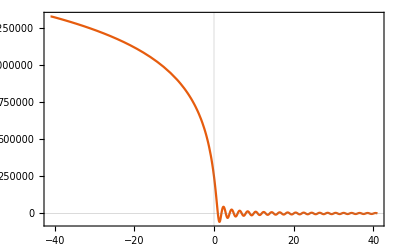

```mathematica
Plot[{ϕC[t]},{t, ti, tf}]
```

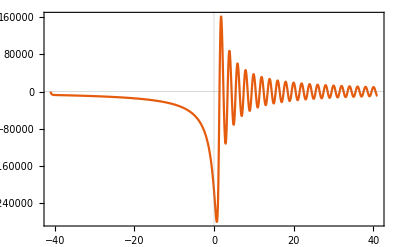

```mathematica
Plot[{ϕC'[t]},{t, ti, tf},PlotRange->All]
```

```mathematica
ϕC''[0]
```

-107082.

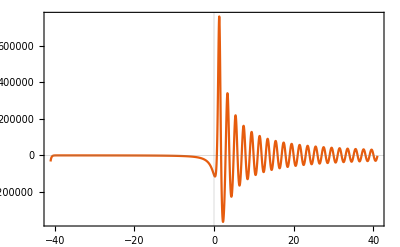

```mathematica
Plot[{ϕC''[t]},{t, ti, tf},PlotRange->All]
```

```mathematica
RC[0]
```

8.66011

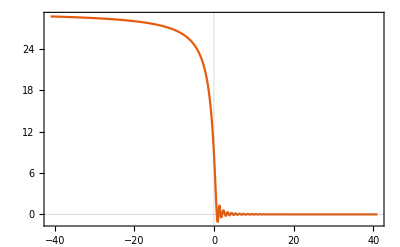

```mathematica
Plot[RC[t],{t, ti,tf},PlotRange->All]
```

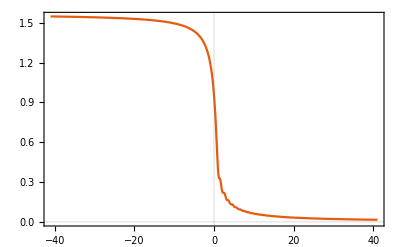

```mathematica
Plot[{HC[t]},{t, ti,tf}]
```

#### Slow-roll parameter

```mathematica
(* In order to see when are we in the slow-roll regime, we have to study the slow-roll parameter ϵ *)

ϵC[t_]=-HC'[t]/HC[t]^2;

ϵ[η_]=ϵC[t]/.t->tt[η];
```

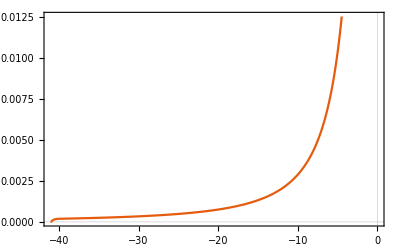

```mathematica
Plot[ϵC[t],{t, ti,0}]
```

#### Scale factor and conformal time

```mathematica
(* We give the scale factor and the relation between cosmological and conformal time *)

aCC[t_]=aaa[t]/.NDSolve[{aaa'[t]==HC[t]*aaa[t], aaa[ti]==1},aaa[t],{t, ti, tf},Method->"StiffnessSwitching"][[1,1]];
aC[t_]=aCC[t]/aCC[tf]*175;


ηη0[t_]=ηηη[t]/.NDSolve[{ηηη'[t]==1/aC[t],ηηη[0]==0},ηηη[t],{t, ti, tf},Method->"StiffnessSwitching"][[1,1]];

ηη[t_]=ηη0[t];

ηi=ηη[ti];
ηf=ηη[tf];

(*table=ParallelTable[{ηη[t],t},{t, ti,tf,100}];*)
table=ParallelTable[{ηη[t],t},{t, ti,tf,0.01}];
tt=Interpolation[table, InterpolationOrder->6];

a[η_]=aC[t]/.t->tt[η];
```

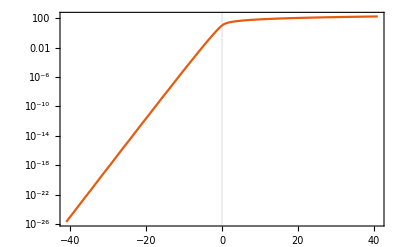

```mathematica
LogPlot[aC[t],{t, ti, tf},PlotRange->All]
```

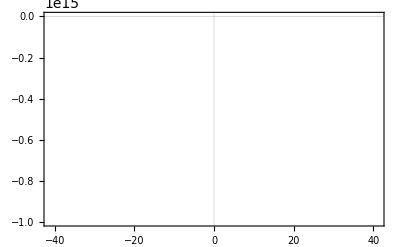

```mathematica
Plot[{ηη[t]},{t, ti, tf}]
```

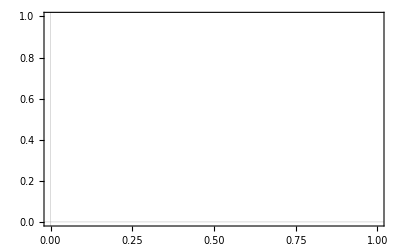

```mathematica
Plot[{tt[η]},{η,ηη[ti],0},PlotRange->All]
```

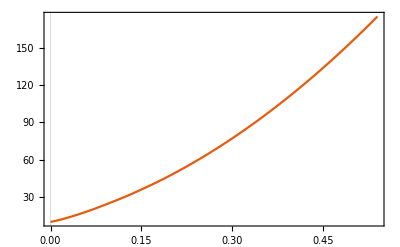

```mathematica
Plot[a[η],{η,0,ηf},PlotRange->All]
```

#### Inflaton field and the Ricci scalar in terms of η

```mathematica
(* Let us give the inflaton time evolution *)

ϕ[η_]=ϕC[t]/.t->tt[η];

(* We give the Ricci scalar *)

R[η_]=8*Pi/MP^2*(4*VS[ϕ[η]] - D[ϕ[η],{η,1}]^2/a[η]^2);
(*Ra[η_]=8*Pi/MP^2*(2*mϕ^2*ϕa[η]^2 - D[ϕa[η],{η,1}]^2/aan[η]^2)*)
RAvg[η_]=0.8R[0.5]/tt[η]^2;
```

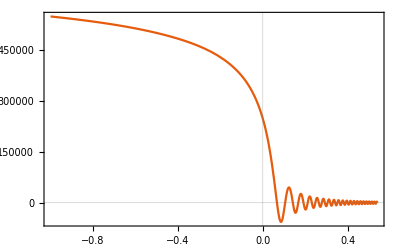

```mathematica
Plot[{ϕ[η]},{η, -1, ηf}]
```

InterpolatingFunction::dmval: Input value {-2.63512×10^25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-2.63512×10^25} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-2.74486×10^25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-2.74486×10^25} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-2.85838×10^25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {-2.85838×10^25} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

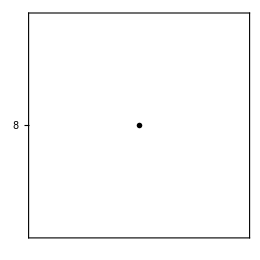

```mathematica
Plot[{ϕ[η]},{η,180, 240},AspectRatio->1,BaseStyle->texStyle,FrameLabel->{{MaTeX["m_{\\phi}^{-1}\\phi(\\eta)",FontSize->14],}, {MaTeX["m_{\\phi}\\eta",FontSize->14],}},FrameTicks->{{{0, {2*10^5,2}, {4*10^5,4}, {6*10^5,6},{8*10^5,8}}, None},{{180, 200, 220,240},None}},FrameTicksStyle->Directive[Black, FontSize->11],PlotRangeClipping->False,PlotStyle->{CoolColors[[1]]},Epilog->Text[MaTeX["(\\times 10^5)",FontSize->10],{-2.7,8*10^5}],ImageSize->260, PlotRange->All]
```

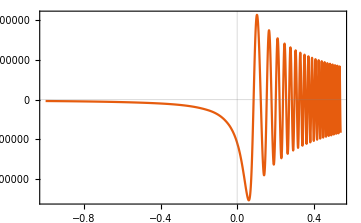

```mathematica
Plot[ϕ'[η],{η, -1, ηf},PlotRange->All]
```

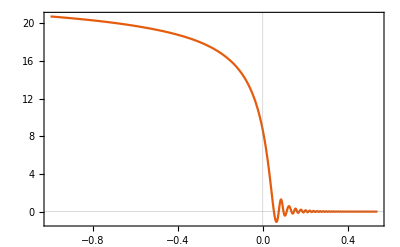

```mathematica
Plot[{R[η]},{η, -1,ηf}, PlotRange->All]
```

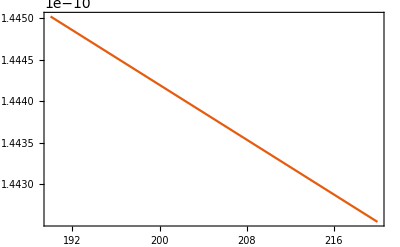

```mathematica
Plot[R[η],{η, 190,220}, PlotRange->All]
```

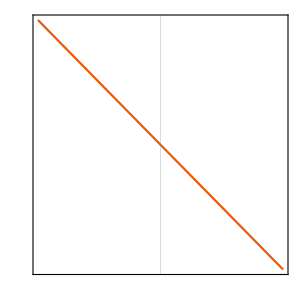

```mathematica
Plot[{RC[t]},{t,-20, 20},AspectRatio->1,BaseStyle->texStyle,FrameLabel->{{MaTeX["R(t)[m_{\\phi}]",FontSize->14],}, {MaTeX["m_{\\phi}t",FontSize->14],}},FrameTicks->{{{{0,MaTeX["0"]},{200,MaTeX["200"]},{400,MaTeX["400"]}}, None},{{{-10,MaTeX["-10"]},{0,MaTeX["0"]},{10,MaTeX["10"]},{20,MaTeX["20"]},{30,MaTeX["30"]},{40,MaTeX["40"]}},None}},ImageSize->300,PlotRange->All]
```

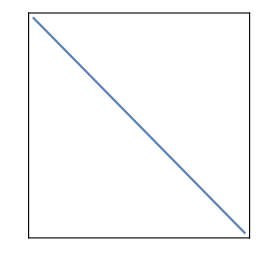

```mathematica
Plot[{R[η]},{η,190, 220},AspectRatio->1,BaseStyle->texStyle,FrameLabel->{{MaTeX["m_{\\phi}^{-2} R(\\eta)",FontSize->14],}, {MaTeX["m_{\\phi}\\eta",FontSize->14],}},FrameTicks->{{{0,5,10,15,20}, None},{{-2,-1,0,1,2,3,4},None}},FrameTicksStyle->Directive[Black, FontSize->11],PlotStyle->{CoolColors[[1]]},ImageSize->260,PlotRange->All]
```

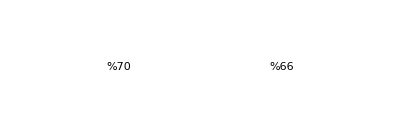

```mathematica
GraphicsRow[{%70,%66}]
```

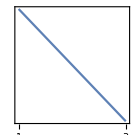

```mathematica
Plot[{R[η]},{η,1, 3},AspectRatio->1,BaseStyle->texStyle,FrameTicks->{{{-0.25, 0, 0.25, 0.50}, None},{{1,2,3},None}},FrameTicksStyle->Directive[Black, FontSize->12],PlotStyle->{CoolColors[[1]]},ImageSize->135,PlotRange->{{0.97,3.03},All}]
```

```mathematica
R[1]
```

1.46044×10^-10

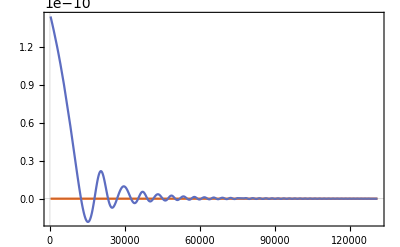

```mathematica
Plot[{RAvg[η],R[η]},{η,250,ηf},PlotRange->All]
```

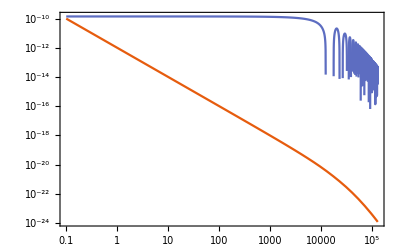

```mathematica
LogLogPlot[{RAvg[η],R[η]},{η,0.1,ηf},PlotRange->Automatic]
```

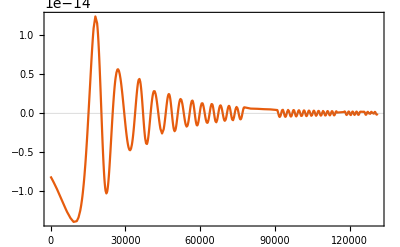

```mathematica
Plot[R'[η],{η, -0.1,ηf}, PlotRange->All]
```

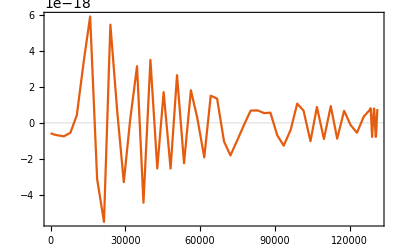

-Graphics-

-Graphics-

-Graphics-

```mathematica
Plot[R''[η],{η, -0.1,ηf}, PlotRange->All]
```

### T-model

#### Solve for the inflaton field

```mathematica
(* Let us give the inflaton time evolution *)

(* First, the initial conditions *)

ti=-50*10^5/rMP;
tf=2*10^2*10^5/rMP;

ϕi=1.0877*MP;
dϕi=0;

(* Out of SR, we have to solve this numerically *)

HC[t_]=Sqrt[4*Pi/(3*MP^2)*(ϕn'[t]^2 + 2*VT[ϕ]/.ϕ->ϕn[t])];
EoM[t_]=ϕn''[t]+3*HC[t]*ϕn'[t] + dVT[ϕ]/.ϕ->ϕn[t];
ϕC[t_]=ϕn[t]/.NDSolve[{EoM[t]==0, ϕn[ti]==ϕi, ϕn'[ti]==dϕi}, {ϕn}, {t, ti, tf}][[1,1]];

(* We give the Ricci scalar for both regimes *)

RC[t_]=8*Pi/MP^2*(4*VS[ϕC[t]] - ϕC'[t]^2);
Ri=RC[ti];
```

```mathematica
NDSolve[{EoMS[t]==0, ϕn[ti]==ϕi, ϕn'[ti]==dϕi}, {ϕn}, {t, ti, tf}]
```

{{ϕn→InterpolatingFunction[…]}}

```mathematica
(* The time-dependent hubble rate is given by the inflaton field *)

HC[t_]=Sqrt[4*Pi/(3*MP^2)*(ϕC'[t]^2 + 2*VS[ϕC[t]])];

Hi=HC[ti];
Hf = HC[0];
```

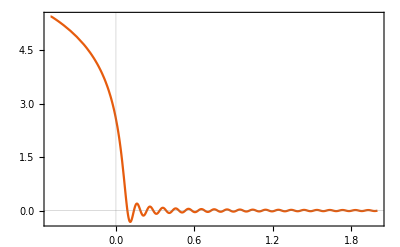

```mathematica
Plot[{ϕC[t]},{t, ti, tf}]
```

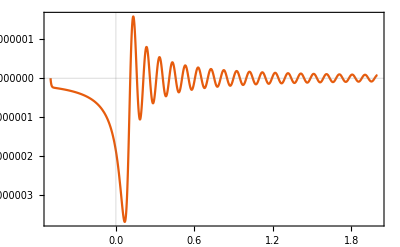

```mathematica
Plot[{ϕC'[t]},{t, ti, tf},PlotRange->All]
```

```mathematica
ϕC''[0]
```

-2.04682×10^-12

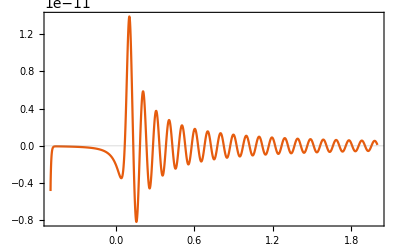

```mathematica
Plot[{ϕC''[t]},{t, ti, tf},PlotRange->All]
```

```mathematica
RC[0]
```

3.78898×10^-10

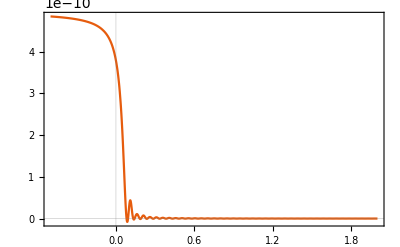

```mathematica
Plot[RC[t],{t, ti,tf},PlotRange->All]
```

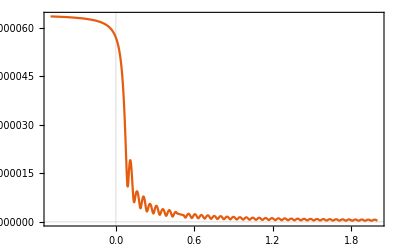

```mathematica
Plot[{HC[t]},{t, ti,tf}]
```

#### Slow-roll parameter

```mathematica
(* In order to see when are we in the slow-roll regime, we have to study the slow-roll parameter ϵ *)

ϵC[t_]=-HC'[t]/HC[t]^2;

ϵ[η_]=ϵC[t]/.t->tt[η];
```

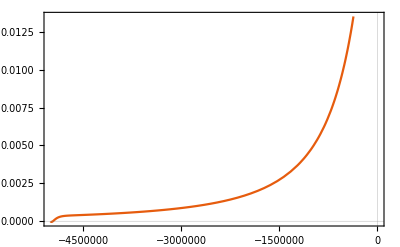

```mathematica
Plot[ϵC[t],{t, ti,0}]
```

#### Scale factor and conformal time

```mathematica
(* We give the scale factor and the relation between cosmological and conformal time *)

aCC[t_]=aaa[t]/.NDSolve[{aaa'[t]==HC[t]*aaa[t], aaa[ti]==1},aaa[t],{t, ti, tf},Method->"StiffnessSwitching"][[1,1]];
aC[t_]=aCC[t]/aCC[tf]*175;


ηη0[t_]=ηηη[t]/.NDSolve[{ηηη'[t]==1/aC[t],ηηη[0]==0},ηηη[t],{t, ti, tf},Method->"StiffnessSwitching"][[1,1]];

ηη[t_]=ηη0[t];

ηi=ηη[ti];
ηf=ηη[tf];

table=ParallelTable[{ηη[t],t},{t, ti,tf,100}];
tt=Interpolation[table, InterpolationOrder->6];

a[η_]=aC[t]/.t->tt[η];
```

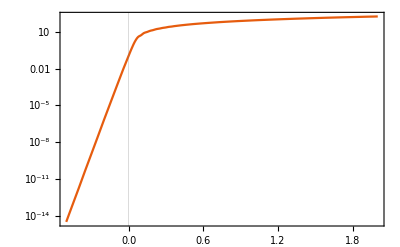

```mathematica
LogPlot[aC[t],{t, ti, tf},PlotRange->All]
```

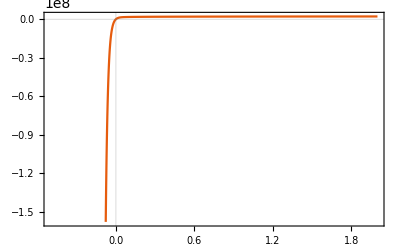

```mathematica
Plot[{ηη[t]},{t, ti, tf}]
```

```mathematica
Plot[{tt[η]},{η,ηη[ti],0},PlotRange->All]
```

-Graphics-

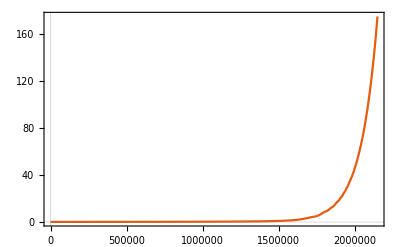

```mathematica
Plot[a[η],{η,0,ηf},PlotRange->All]
```

#### Inflaton field and the Ricci scalar in terms of η

```mathematica
(* Let us give the inflaton time evolution *)

ϕ[η_]=ϕC[t]/.t->tt[η];

(* We give the Ricci scalar *)

R[η_]=8*Pi/MP^2*(4*VT[ϕ[η]] - D[ϕ[η],{η,1}]^2/a[η]^2);
(*Ra[η_]=8*Pi/MP^2*(2*mϕ^2*ϕa[η]^2 - D[ϕa[η],{η,1}]^2/aan[η]^2)*)
RAvg[η_]=0.8R[200]/tt[η]^2;
```

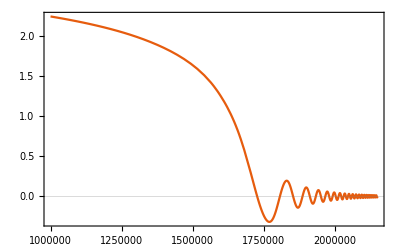

```mathematica
Plot[{ϕ[η]},{η, 10^6, ηf}]
```

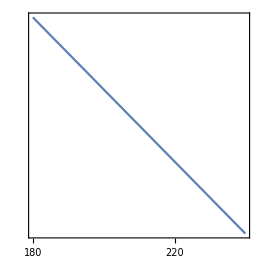

```mathematica
Plot[{ϕ[η]},{η,180, 240},AspectRatio->1,BaseStyle->texStyle,FrameLabel->{{MaTeX["m_{\\phi}^{-1}\\phi(\\eta)",FontSize->14],}, {MaTeX["m_{\\phi}\\eta",FontSize->14],}},FrameTicks->{{{0, {2*10^5,2}, {4*10^5,4}, {6*10^5,6},{8*10^5,8}}, None},{{180, 200, 220,240},None}},FrameTicksStyle->Directive[Black, FontSize->11],PlotRangeClipping->False,PlotStyle->{CoolColors[[1]]},Epilog->Text[MaTeX["(\\times 10^5)",FontSize->10],{-2.7,8*10^5}],ImageSize->260, PlotRange->All]
```

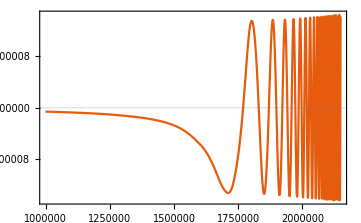

```mathematica
Plot[ϕ'[η],{η, 10^6, ηf},PlotRange->All]
```

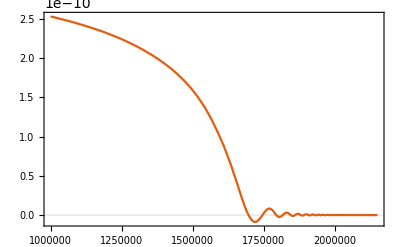

```mathematica
Plot[{R[η]},{η, 10^6,ηf}, PlotRange->All]
```

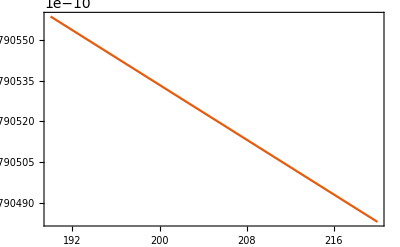

```mathematica
Plot[R[η],{η, 190,220}, PlotRange->All]
```

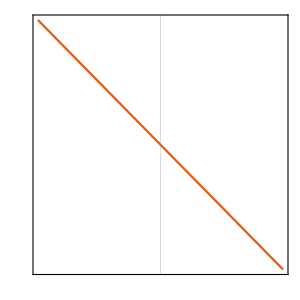

```mathematica
Plot[{RC[t]},{t,-20, 20},AspectRatio->1,BaseStyle->texStyle,FrameLabel->{{MaTeX["R(t)[m_{\\phi}]",FontSize->14],}, {MaTeX["m_{\\phi}t",FontSize->14],}},FrameTicks->{{{{0,MaTeX["0"]},{200,MaTeX["200"]},{400,MaTeX["400"]}}, None},{{{-10,MaTeX["-10"]},{0,MaTeX["0"]},{10,MaTeX["10"]},{20,MaTeX["20"]},{30,MaTeX["30"]},{40,MaTeX["40"]}},None}},ImageSize->300,PlotRange->All]
```

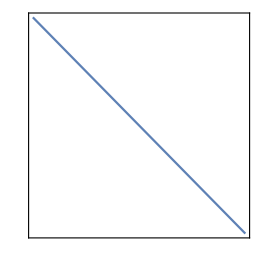

```mathematica
Plot[{R[η]},{η,190, 220},AspectRatio->1,BaseStyle->texStyle,FrameLabel->{{MaTeX["m_{\\phi}^{-2} R(\\eta)",FontSize->14],}, {MaTeX["m_{\\phi}\\eta",FontSize->14],}},FrameTicks->{{{0,5,10,15,20}, None},{{-2,-1,0,1,2,3,4},None}},FrameTicksStyle->Directive[Black, FontSize->11],PlotStyle->{CoolColors[[1]]},ImageSize->260,PlotRange->All]
```

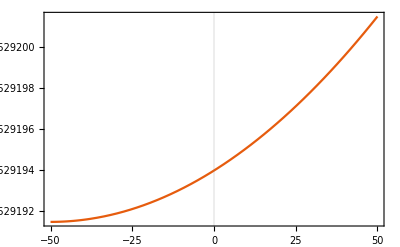

```mathematica
GraphicsRow[{%70,%66}]
```

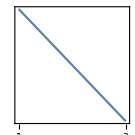

```mathematica
Plot[{R[η]},{η,1, 3},AspectRatio->1,BaseStyle->texStyle,FrameTicks->{{{-0.25, 0, 0.25, 0.50}, None},{{1,2,3},None}},FrameTicksStyle->Directive[Black, FontSize->12],PlotStyle->{CoolColors[[1]]},ImageSize->135,PlotRange->{{0.97,3.03},All}]
```

```mathematica
R[1]
```

2.9791×10^-10

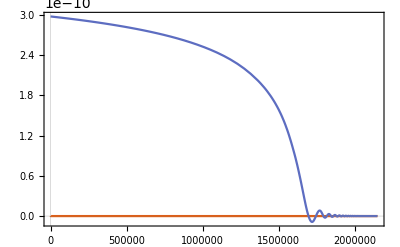

```mathematica
Plot[{RAvg[η],R[η]},{η,250,ηf},PlotRange->All]
```

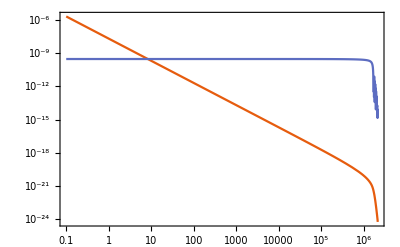

```mathematica
LogLogPlot[{RAvg[η],R[η]},{η,0.1,ηf},PlotRange->Automatic]
```

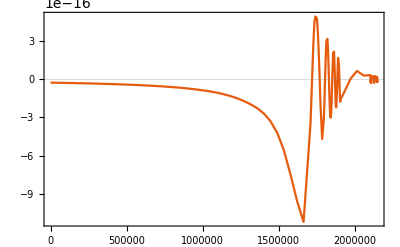

```mathematica
Plot[R'[η],{η, -0.1,ηf}, PlotRange->All]
```

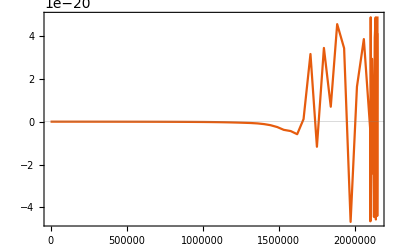

```mathematica
Plot[R''[η],{η, -0.1,ηf}, PlotRange->All]
```

Higgs field - Spectator within Hartree approximation

```mathematica
(* First, we define the running coupling *)

(*λH[η_,k_,ξH_]:=0.01*Sign[hSM-h2[η,k,ξH]]*)
λH[η_,k_,ξH_]:=0.01;
hSM =10^10/rMP;

h2[η_,k_,ξH_]:=10^8/rMP (* Need to properly compute it *)

(* We define the mode frequency *)

ωH[η_, k_,ξH_]=Sqrt[k^2 + a[η]^2*(3*λH[η,k,ξH]*h2[η,k,ξH] + (ξH-1/6)*R[η])];
dωH[η_, k_,ξ_]=D[ωH[η,k,ξH],{η,1}];
d2ωH[η_, k_,ξ_]=D[ωH[η,k,ξH],{η,2}];

(* Also let us give the BD modes *)

ωdS[η_, k_,μ_]=Sqrt[k^2 + μ^2/η^2];
ν = Sqrt[1/4 - μ^2];
A[k_]=Sqrt[Pi/(2*k)*Exp[I*Pi*(ν+1/2)]];
hBD[η_, k_,μ_]=Sqrt[k*Sqrt[η^2]]*A[k]*HankelH1[ν,k*Sqrt[η^2]];
dhBD[η_, k_, μ_]=D[hBD[η, k,μ],{η, 1}];
```

```mathematica
(* We use the analytical solution for the SR region as initial condition. This function has to be such that in the limit it coincides with the de Sitter solution, so the integration constant is different now. *)

τ[η_,k_,ξH_]=
ωH[η,k,ξH]/ωdS[η,k,μ]*(η-
-ηSR)+ηSR-1/Hi/.μ->Sqrt[(3*λH[η,k,ξH]*h2[η,k,ξH]+ξH*Ri)/Hi^2-2];

(*hSR[η_,k_,ξH_]:=Sqrt[-k*τ[η,k,ξH]]*A[k]*HankelH1[ν,k*-τ[η,k,ξH]]/.μ->Sqrt[(3*λH[η,k,ξH]+ξH*Ri)/Hi^2-2];*)
hSR[η_,k_,ξH_]:=Sqrt[-k*η]*A[k]*HankelH1[ν,k*-η]/.μ->Sqrt[(3*λH[η,k,ξH]*h2[η,k,ξH]+ξH*Ri)/Hi^2-2];
dhSR[η_,k_,ξH_]=D[hSR[η,k,ξH],{η,1}];
d2hSR[η_,k_,ξH_]=D[hSR[η,k,ξH],{η,2}];

(* We give the function to be solved *)

FH[η_, k_,ξH_]= D[h1[η], {η, 2}] + ωH[η, k, ξH]^2*h1[η];
```

```mathematica
1/Hi
```

0.646396

```mathematica
τ[-10^7,10^-12,1]//N
```

-1.03254×10^7

```mathematica
ηf
```

0.54053

```mathematica
hSR[-10^7,10^-30,1]
```

768.731-1414.18 ⅈ

```mathematica
hSR[ηSR,1/rMP,1]
```

-4.57611-2.22874 ⅈ

```mathematica
(* We solve the equation numerically *)

(* Let us assume SR is valid up to this point *)
ηSR =-100*rMP;

(* We can compare with the real equation, out of slow-roll, assuming dS is also valid up to here *)
SolH= ParametricNDSolve[{FH[η, k, ξH]==0, h1[ηSR]==hSR[ηSR,k,ξH],h1'[ηSR]==dhSR[ηSR,k,ξH]}, {h1,h1'}, {η, ηSR, ηf},{k,ξH}];

h[η_, k_?NumericQ,ξH_] :=h[η, k,ξH] =h1[k,ξH][η]/.SolH;
dh[η_, k_,ξH_]:=dh[η, k,ξH] =h1'[k,ξH][η]/.SolH;
d2h[η_, k_,ξH_]:=ND[h[η0, k,ξH], {η0, 2},η];
```

```mathematica
h[ηf,0.1/rMP,1]
```

-0.0117996+0.0365829 ⅈ

```mathematica
(* We define the "exact" adiabatic vacuum *)

uH[η_,k_,ξH_]=1/Sqrt[ωH[η,k,ξH]];

duH[η_,k_,ξH_]=-1/Sqrt[ωH[η,k,ξH]]*(I*ωH[η,k,ξH] +dωH[η,k,ξH]/(2*ωH[η,k,ξH]));
```

```mathematica
(* We define Bogoliubov coefficients for the analytic SR solution *)

βH[η_,k_,ξH_]=(uH[η, k,ξH]*dh[η,k,ξH] - duH[η, k,ξH]*h[η, k,ξH])/(2*I) ;
```

```mathematica
(* Lastly we define the coefficients we are interested in *)

βH2[η_,k_,ξ_]=βH[η,k,ξ]*Conjugate[βH[η,k,ξ]];
```

```mathematica
Clear[βH2]
```

```mathematica
βH2[ηf,0.1/rMP,1/6]
```

0.0000643476+0. ⅈ

```mathematica
table1=ParallelTable[{10^k/rMP,10^(2*k)/rMP^2*βH2[ηf,10^k/rMP,1/6]},{k,-2,1.5,0.01}];
```

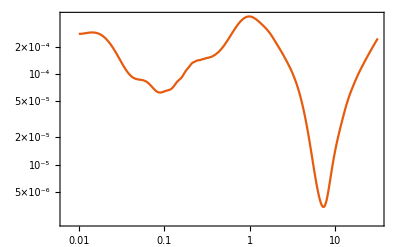

-Graphics-

```mathematica
ListLogLogPlot[table1,PlotRange->All,Joined->True]
```

```mathematica
table2=ParallelTable[{10^k,βH2[ηf,10^k/rMP,1]},{k,-2,1.5,0.01}];
```

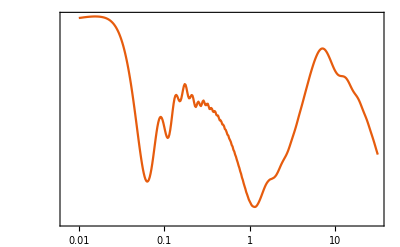

```mathematica
ListLogLogPlot[table2,PlotRange->All,Joined->True]
```

```mathematica
(* Let us compute the energy densities *)

ρϕ[t_]:=1/2*ϕC'[t]^2+VS[phi]+1/2*λϕ*hC[t]^2*ϕC [t]^2/.phi->ϕC[t]
ρϕApprox[t_]:=1/2*ϕC'[t]^2+VS[phi]/.phi->ϕC[t]
```

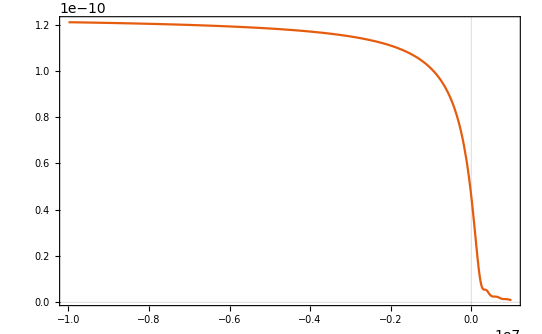

```mathematica
Plot[{ρϕApprox[t],ρϕ[t]},{t,ti,tf},PlotRange->All]
```

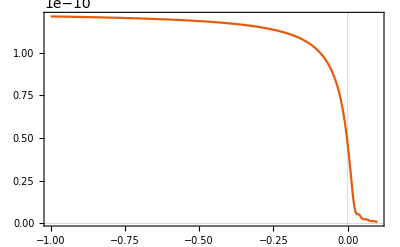

```mathematica
Plot[{ρϕApprox[t]},{t,ti,tf},PlotRange->All]
```

Scalar mode equation and particle production - Starobinsky

### Mode equation for the 2nd region - Numerical inflation, escape and reheating

```mathematica
(* We define the mode frequency *)

ω[η_, k_,m_,ξ_]=Sqrt[k^2 + a[η]^2*(m^2 + (ξ-1/6)*R[η])];
dω[η_, k_,m_,ξ_]=D[ω[η,k,m,ξ],{η,1}];
d2ω[η_, k_,m_,ξ_]=D[ω[η,k,m,ξ],{η,2}];

(* We also give the de Sitter frequency for computing the approximate solution during SR *)

ωdS[η_, k_,μ_]=Sqrt[k^2 + μ^2/η^2];

(* Also let us give the BD modes *)

ν = Sqrt[1/4 - μ^2];
A[k_]=Sqrt[Pi/(2*k)*Exp[I*Pi*(ν+1/2)]];
vBD[η_, k_,μ_]=Sqrt[k*Sqrt[η^2]]*A[k]*HankelH1[ν,k*Sqrt[η^2]];
dvBD[η_, k_, μ_]=D[vBD[η, k,μ],{η, 1}];
```

```mathematica
(* We use the analytical solution for the SR region as initial condition. This function has to be such that in the limit it coincides with the de Sitter solution, so the integration constant is different now. *)

τ[η_,k_,m_,ξ_]=
ω[η,k,m,ξ]/ωdS[η,k,μ]*(η-
-ηSR)+ηSR-1/Hi/.μ->Sqrt[(m^2+ξ*Ri)/Hi^2-2];

(*vSR[η_,k_,m_,ξ_]:=vSR[η,k,m,ξ]=Sqrt[-k*τ[η,k,m,ξ]]*A[k]*HankelH1[ν,k*-τ[η,k,m,ξ]]/.μ->Sqrt[(m^2+ξ*Ri)/Hi^2-2];*)
vSR[η_,k_,m_,ξ_]:=vSR[η,k,m,ξ]=Sqrt[-k*η]*A[k]*HankelH1[ν,-k*η]/.μ->Sqrt[(m^2+ξ*Ri)/Hi^2-2];
dvSR[η_,k_,m_,ξ_]=D[vSR[η,k,m,ξ],{η,1}];
d2vSR[η_,k_,m_,ξ_]=D[vSR[η,k,m,ξ],{η,2}];

(* We give the function to be solved *)

F[η_, k_,m_,ξ_]= D[v1[η], {η, 2}] + ω[η, k, m,ξ]^2*v1[η];
```

```mathematica
Clear[vSR]
```

```mathematica
vSR[ηSR,10^-2,10^-1,1/6]*Conjugate[dvSR[ηSR,10^-2,10^-1,1/6]]-Conjugate[vSR[ηSR,10^-2,10^-1,1/6]]*dvSR[ηSR,10^-2,10^-1,1/6]
```

0.+2. ⅈ

```mathematica
-100*rMP
```

-2.435×10^7

```mathematica
(* We solve the equation numerically *)

(* Let us assume SR is valid up to this point *)
ηSR =-100*rMP;

(* We can compare with the real equation, out of slow-roll, assuming dS is also valid up to here *)
Sol= ParametricNDSolve[{F[η, k, m,ξ]==0, v1[ηSR]==vSR[ηSR,k,m,ξ],v1'[ηSR]==dvSR[ηSR,k,m,ξ]}, {v1,v1'}, {η, ηSR, ηf},{k,m,ξ}];

v[η_, k_?NumericQ,m_,ξ_] :=v[η, k,m,ξ] =v1[k,m,ξ][η]/.Sol;
dv[η_, k_,m_,ξ_]:=dv[η, k,m,ξ] =v1'[k,m,ξ][η]/.Sol;
d2v[η_, k_,m_,ξ_]:=ND[v[η0, k,m,ξ], {η0, 2},η];
```

```mathematica
Clear[v,dv]
```

```mathematica
ηf
```

0.54053

```mathematica
v[ηf,10^-4,10^-4,1]*Conjugate[ND[v[η,10^-4,10^-4,1],η,ηf]]-Conjugate[v[ηf,10^-4,10^-4,1]]*ND[v[η,10^-4,10^-4,1],η,ηf]
```

InterpolatingFunction::dmval: Input value {1.54053} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04053} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.79053} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0.+2.00027 ⅈ

```mathematica
v[ηf,10^-3,10^-4,1]*Conjugate[dv[ηf,10^-3,10^-4,1]]-Conjugate[v[ηf,10^-3,10^-4,1]]*dv[ηf,10^-3,10^-4,1]
```

0.+2.00266 ⅈ

```mathematica
(* We define the "exact" adiabatic vacuum *)

u[η_,k_,m_,ξ_]=1/Sqrt[ω[η,k,m,ξ]];

du[η_,k_,m_,ξ_]=-1/Sqrt[ω[η,k,m,ξ]]*(I*ω[η,k,m,ξ] +dω[η,k,m,ξ]/(2*ω[η,k,m,ξ]));
```

```mathematica
(* We define vacuum with the mean R *)

ωAv[η_, k_,m_,ξ_]=Sqrt[k^2 + a[η]^2*(m^2 +(ξ-1/6)*RAvg[η])];
dωAv[η_, k_,m_,ξ_]=D[ωAv[η,k,m,ξ],{η,1}];

uAv[η_,k_,m_,ξ_]=1/Sqrt[ωAv[η,k,m,ξ]];
duAv[η_,k_,m_,ξ_]=-1/Sqrt[ωAv[η,k,m,ξ]]*(I*ωAv[η,k,m,ξ] + D[ωAv[η,k,m,ξ],{η, 1}]/(2*ωAv[η,k,m,ξ]));
```

```mathematica
(* We define Bogoliubov coefficients for the analytic SR solution *)

β[η_,k_,m_,ξ_]=(u[η, k,m,ξ]*dv[η,k,m,ξ] - du[η, k,m,ξ]*v[η, k,m,ξ])/(2*I) ;

βAv[η_,k_,m_,ξ_]=(uAv[η, k,m,ξ]*dv[η,k,m,ξ] - duAv[η, k,m,ξ]*v[η, k,m,ξ])/(2*I) ;
```

```mathematica
β[ηf,1,1,1]
```

0.205654+0.317552 ⅈ

```mathematica
βAv[ηf,1,1,1]
```

0.205334+0.317685 ⅈ

```mathematica
(* Lastly we define the coefficients we are interested in *)

β2[η_,k_,m_,ξ_]:=β2[η,k,m,ξ]=β[η,k,m,ξ]*Conjugate[β[η,k,m,ξ]];
β2Av[η_,k_,m_,ξ_]:=β2Av[η,k,m,ξ]=βAv[η,k,m,ξ]*Conjugate[βAv[η,k,m,ξ]];
```

```mathematica
Clear[β2,β2Av]
```

```mathematica
β[ηf,1,10^-4,0.2]
```

148.408+86.5332 ⅈ

```mathematica
table1=ParallelTable[{10^k,10^(2*k)*β2[ηf,10^k,1,1]},{k,-2,2,0.1}];
```

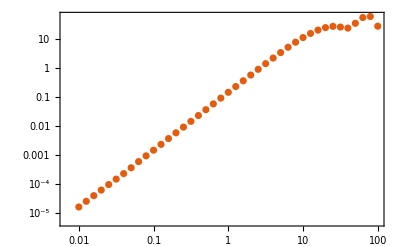

```mathematica
ListLogLogPlot[table1,PlotRange->All]
```

```mathematica
table2=ParallelTable[{10^k/rMP,10^(2*k)/rMP^2*β2Av[ηf,10^k/rMP,1.4,1]},{k,-1,3,0.1}];
```

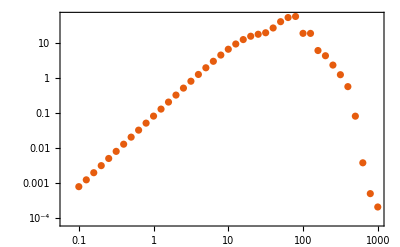

```mathematica
ListLogLogPlot[table2,PlotRange->All]
```

```mathematica
table3=ParallelTable[{10^k/rMP,10^(2*k)/rMP^2*β2[ηf,10^k/rMP,1.8/rMP,1/6]},{k,-2,4,0.1}];
```

$Aborted

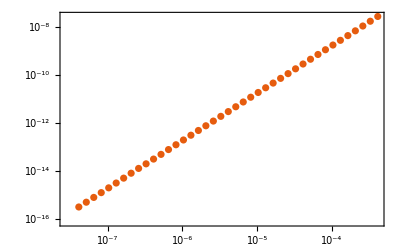

```mathematica
ListLogLogPlot[table3,PlotRange->All]
```